## HumMod 1.6

```mathematica
Clear[s]
```

```mathematica
s=Solve[{n*310.15*8.314 ==(101325/760)*(320 (0.001*t) + 1160 (0.001*t)^2), mw==t/(n*0.001)},{mw,n}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
mw/.s /. {t->70}
```

{48207.9}

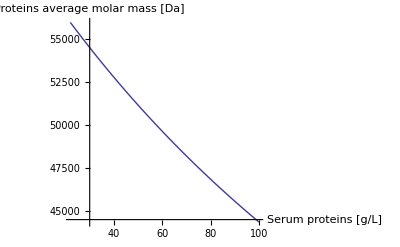

```mathematica
Plot[mw/.s,{t,22,100},PlotRange->Full,AxesLabel->{"Serum proteins [g/L]","Proteins average molar mass [Da]"}]
```

0.0165452 m+0.0000599762 m^2

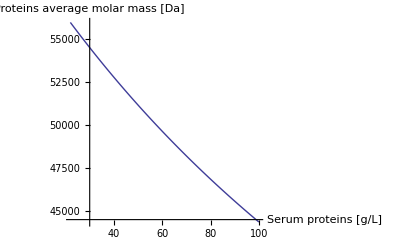

```mathematica
n=(320*101325/760)/(310.15*8.314)0.001*m+(1160*101325/760)/(310.15*8.314)(0.001*m)^2

Plot[10^3/(0.016545+0.000059976m),{m,22,100},PlotRange->Full,AxesLabel->{"Serum proteins [g/L]","Proteins average molar mass [Da]"}]
```

```mathematica
Molar mass of globulins (if alb=0.63 mmol/l)
```

```mathematica
Solve[{nglb*310.15*8.314 + 0.63*310.15*8.314==(101325/760)*(320 (0.001*t) + 1160 (0.001*t)^2), mwglb==(t-42)/(nglb*0.001)},{mwglb,nglb}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{mwglb→(2.33301×10^12 (-42.+t))/(-1.46979×10^9+3.86×10^7 t+139925. t^2),nglb→4.28631×10^-10 (-1.46979×10^9+3.86×10^7 t+139925. t^2)}}

```mathematica
Clear[mwglb,nglb]
```

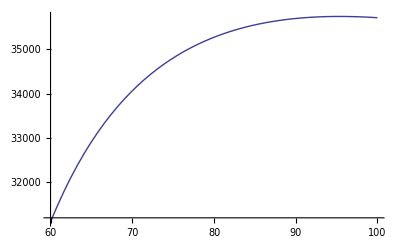

```mathematica
Plot[(2.333007376190476*^12 (-42.+t))/(-1.469794647*^9+3.86*^7 t+139925. t^2),{t,60,100}]
```

## Model with mwalb=66,5kDa and mwglb=34.5kDa

```mathematica
sol=Solve[{ (4.835248448063163*^8)/(8000.+29. t)==t/(((1-r) t)/34500+(r t)/66500)},r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-5.30208×10^-10 (-1.6822×10^9+8.11005×10^6 t)}}

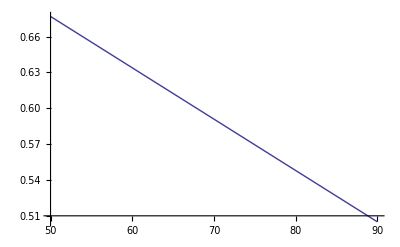

```mathematica
Plot[r/. sol,{t,50,90}, PlotRange->Full]
```

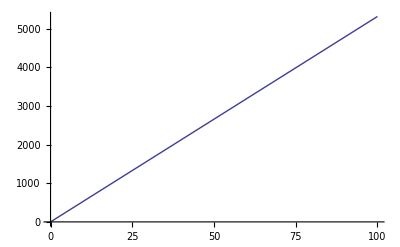

```mathematica
Plot[(((alb/66500)+glb/34500)*1000)*T*8.314/.{T->310.15,alb->t*0.6,glb->t*0.4},{t,0,100} ]
```

```mathematica
(tt/(((alb/66500)+glb/34500)*1000))/.{tt->t,alb->t*r,glb->t*(1-r)}
```

t/(1000 (((1-r) t)/34500+(r t)/66500))

```mathematica
Clear[t]
```

```mathematica
Plot[(tt/(((alb/66500)+glb/34500)*1000))/.{tt->t,alb->t*0.6,glb->t*0.4},{t,50,51} ]
```

-Graphics-

## Nitta S, Ohnuki T, Ohkuda K, Nakada T, and Staub NC. The corrected protein equation to estimate plasma colloid osmotic pressure and its development on a nomogram. Tohoku J Exp Med 135: 43–49, 1981.

```mathematica
Clear[t,alb]
```

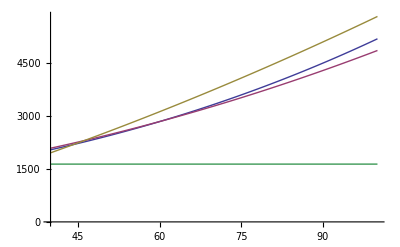

```mathematica
Plot[{(101325/760)((alb/tt(2.8 tt + 0.18 tt^2 + 0.012 tt^3 )+(tt - alb)/tt(0.9 tt+ 0.12 tt^2 + 0.004 tt^3)))/. {alb->4.2, tt->t*0.1},
(101325/1033)(alb/t(0.382 t + 0.0028 t^2 +0.000013 t^3) + (t - alb)/t(0.119 t + 0.0016 t^2))/. {alb->42},
(101325/760)*(320 (0.001*t) + 1160 (0.001*t)^2),
0.63*(273.15+39)*8.314
}, {t,40,100}, PlotRange->{0,Full}]
```

```mathematica
Clear[ss]
```

```mathematica
ss=Solve[{nglb*(273.15+39)*8.314 + 0.63*(273.15+39)*8.314==(101325/760)(4.2/tt(2.8 tt + 0.18 tt^2 + 0.012 tt^3 )+(tt - 4.2)/tt(0.9 tt+ 0.12 tt^2 + 0.004 tt^3)),tt*10==mwglb*nglb*0.001},{nglb,mwglb}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{nglb→4.25885×10^-10 (-5.16685×10^8+1.3896×10^8 tt+1.8528×10^7 tt^2+482500. tt^3),mwglb→(2.34805×10^13 tt)/(-5.16685×10^8+1.3896×10^8 tt+1.8528×10^7 tt^2+482500. tt^3)}}

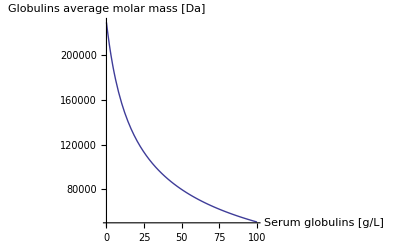

```mathematica
Plot[mwglb/.ss/.{tt->(4.2+0.1*glb)},{glb,0,100},PlotRange->Full,AxesLabel->{"Serum globulins [g/L]","Globulins average molar mass [Da]"}]
```

```mathematica
Solve[
(101325/1033)(alb/t(0.382 t + 0.0028 t^2 +0.000013 t^3) + (t - alb)/t(0.119 t + 0.0016 t^2))/. {alb->0}}, {t,0,50}]
```

### Recalculation of interstitial protein amounts

```mathematica
n[m_,v_]:=(320*101325/760)/(310.15*8.314)*0.001*m+(1160*101325/760)/(310.15*8.314)*(0.001*m)^2/v;
```

```mathematica
n[0.075,0.00340217] (* lower torso (3402.17 ml): 75g of extracellular interstitial proteins *)
```

0.00134005

```mathematica
n[0.150,0.00567029] (* middle torso (5670.29 ml): 150g of extracellular interstitial proteins *)
```

0.00271976

```mathematica
n[0.075,0.00226812] (* upper torso (2268.12 ml): 75g of extracellular interstitial proteins *)
```

0.00138963

```mathematica
n[0.210,0.003020] (* blood plasma (3020 ml): 210g of extracellular interstitial proteins *)
```

0.0043503

```mathematica
Concentration (mmol/l)
```

```mathematica
n[0.075,0.00340217]/0.00340217
```

0.393881

```mathematica
n[0.150,0.00567029]/0.00567029
```

0.479652

```mathematica
n[0.075,0.00226812]/0.00226812
```

0.612679

```mathematica
n[0.210,0.003020]/0.003020
```

1.4405